```mathematica
SetDirectory["~/Desktop/surface_gf/surface_spct_wsm"];
hrfile = Import["4_weyl_hr.dat"] ;
(*hrfile = Import["weyl_hr.dat"] ;*)
norb = 4;
kernum = 16;
For [i = -1, i<= 1, i++,
For [j = -1, j<= 1, j++,
For [k = -1, k<= 1, k++,
For [m = 1, m<= norb, m++,
For [n = 1, n<= norb, n++,

tt[i][j][k][m][n] = 0;
]]]]]
For [i = 1, i<= Length[hrfile], i++,
tt[hrfile[[i,1]]][hrfile[[i,2]]][hrfile[[i,3]]][hrfile[[i,4]]][hrfile[[i,5]]] = hrfile[[i,6]]+I*hrfile[[i,7]]]

(*Nx = 99;
Ny = 99;
Nz = 99;*)

(*For[jx=0,jx<=Nx,jx++,
For[jz=0,jz<=Nz,jz++,
kx=(( 2*jx /Nx-1) *Pi);
kz=((2*jz /Nz-1 )*Pi);*)
CloseKernels[];
LaunchKernels[10];
ham[kx_,ky_,kz_]:=(*Parallel*)Table[
(*kx=(( 2*jx /Nx-1) *Pi);
ky=(( 2*jx /Ny-1) *Pi);
kz=((2*jz /Nz-1 )*Pi);*)
(*ky = Pi;*)
(*For[m=1,m<=4,m++,
For[n=1,n<=4,n++,*)
txz(*[jx][jz][m][n]*)=Sum[(tt[cx][cy][cz][m][n])*Exp[I*(cx*kx+cy*ky+cz*kz)],{cx,-1,1},{cy,-1,1},{cz,-1,1}]/Sqrt[2*Pi]^3;
txz(*[jx][jz][m][n]*),
(*{jx,0,Nx},{jy,0,Ny},{jz,0,Nz},*){m,1,norb},{n,1,norb}];
Clear[hrfile];
```

```mathematica
kkm = 20;
afb =0.005;
x = 0.0;
Gk [kx_,ky_,kz_]:= Inverse[(x+I*afb)*IdentityMatrix[norb]-ham[kx,ky,kz]];
Gkr[kx_,ry_, kz_] := Sum[Exp[I*(ky*ry)]*Gk[kx,ky,kz],{ky,-Pi,Pi,Pi/kkm}]/kkm;
Vimp=100.0;
Himp=Vimp*IdentityMatrix[norb];
Tmatrix[kx_,kz_]:=Inverse[(IdentityMatrix[norb]-Himp . Gkr[kx,0.0,kz])] . Himp;
Gfull[kx_,kz_]:=Gkr[kx,0.0,kz]+(Gkr[kx,-1,kz] . Tmatrix[kx,kz]) . Gkr[kx,1,kz]
```

```mathematica
(*-Im[Tr[Gfull[-Pi,-Pi]]]/Pi*)
```

```mathematica
CloseKernels[];
LaunchKernels[kernum];
A = Flatten[ParallelTable[{kx,kz,-1.0/Pi*Im[Tr[Gfull[kx,kz]]]},{kx,-Pi/2,Pi/2,Pi/kkm},{kz,-Pi/2,Pi/2,Pi/kkm}],1];
(*A = Flatten[ParallelTable[{kx,kz,-1.0/Pi*Im[Gfull[kx,kz][[1,1]]+Gfull[kx,kz][[2,2]]+Gfull[kx,kz][[3,3]]+Gfull[kx,kz][[4,4]]]},{kx,-Pi/2,Pi/2,Pi/kkm},{kz,-Pi/2,Pi/2,Pi/kkm}],1];*)
```

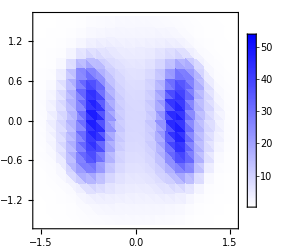

```mathematica
plot =ListDensityPlot[A,PlotRange->All,PlotLegends->Automatic,ColorFunction->(Blend[{White,Blue},#]&),ImageSize->250]
(*Export["plot.png",Rasterize[plot,ImageResolution->300]];*)
```

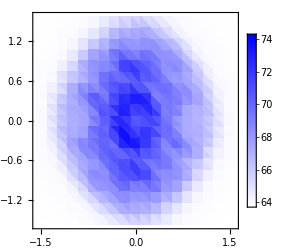

```mathematica
A = Import["/home/quantumworld/Desktop/surface_gf/surface_spct_wsm/calculated_A.dat"];
ListDensityPlot[A,PlotRange->All,PlotLegends->Automatic,ColorFunction->(Blend[{White,Blue},#]&),ImageSize->250]
```